# TF Network Inference from gene expression data after TF perturbation

## Overview

In this lab, you will process actual yeast gene expression taken at time points after the induction (i.e. activation) of a transcription factor (TF). The goal is to determine, for each of 16 TFs, which genes the TF regulates by binding in the promoter region of the gene and affecting its transcription rate. The trick is to do this from gene expression data only, without any data on TF binding locations. Binding location data, obtained using the Transposon Calling Cards method, will be used to test and validate the predictions. Predicting binding location by using only gene expression data is very difficult, so we don’t expect the predictions to be perfect or even near perfect. However, we do expect that the most strongly predicted (TF, target) edges will be enriched for edges supported by binding data.

The overall approach is LASSO, a.k.a L1 regularized or penalized regression. In each regression run, a parameter called lambda is selected by cross-validation. The optimization chooses coefficients that minimize the the sum of the squared errors plus lambda times the sum of the absolute values of the coefficients. This additional term causes the coefficients to shrunken toward zero, increasing the bias and the error on the training data, but decreasing the variance and the error on the new data not used in training.

Note: You must have Mathematica version 12.0 or higher to do this lab. The necessary functions and options don’t exist in earlier versions.

## Coding

This is a larger code base, relative to most other labs (and it took me a lot longer to write than I anticipated)! However, most of the code I wrote is provided for you in  the files tools.m or the netRegression.m. You only have to implement a few key parts of this. There is extensive documentation in netRegression.m, so I won’t go over the provided functions here.

The top level function, inferTFNetLasso, reads in files and sets up a data structure called netObject that stores diverse input, intermediate, and output information for the run. The final return value of inferTFNetLasso is a netObject, which can be queried by calling it on certain strings, as in netObject["geneExpressionMatrix"] , or netObject["rankedEdges"]. Besides reading in files and setting up the netObject, the main thing inferTFNetLasso does is to map netLasso across the genes, so that the expression profile of one gene is passed in on each call to netLasso. The netObject is also passed in to netLasso, which stores intermediate and final results for each gene in it. Beside inferTFNetLasso and  netLasso, no other functions modify the netObject.

### Potentially confusing terminology

The field of linear regression has a lot of synonyms that are potentially confusing. Here is a partial thesaurus to help you through.

The following are all synonyms: penalized regression, shrunken regression, regularized regression. They all refer to methods that shrink parameters toward zero, rather than taking their maximum likelihood estimates, in order to avoid over-fitting to the training data and thereby failing to make accurate predictions on new data not seen during training. Regression without any shrinkage is referred to as ordinary least squares (sometimes OLS) regression.

Synonyms: The LASSO, LASSO regression, L1 penalized (shrunken, regularized) regression. L1 indicates that the sum of the absolute values of the parameters is used for the penalty term, which is added to the sum of squared errors as the objective function for optimizing the parameters. L2 penalized regression adds the sum of squared parameters  instead of the sum of absolute values of parameters. L2 penalized regression, also called ridge regression, is a popular alternative that has different properties from L1.

Synonyms: penalty parameter, shrinkage parameter, lambda. This is a number >= zero that the penalty term is multiplied by before adding it to the error term. In other words, lambda weights the penalty term. A small value of lambda will give results similar to ordinary least squares (no penalty) while a larger value will shrink the coefficients more. (Note that most individual parameters will shrink but some may increase as a result of increasing  lambda.)

Response values, the results you are trying to predict. In our case, the response variable for each individual regression run is the expression level of a particular target gene in many different samples. Each sample, in our case, is a biological sample in which gene expression has been measured. In this lab in particular, each sample measures the expression of all genes shortly after adding a chemical that causes a particular TF to activate. However, the regression is done separately for predicting the expression level of each gene. So the response vector is the expression level of one gene, across all available samples. It’s length is the number of samples.

Synonyms: Predictors matrix, design matrix. This is the input information used to make predictions. It consists of the values for multiple features across multiple samples.  For network inference, each feature is the expression level of a TF. In this lab, we are using 14 features (TFs). By convention, the rows of the design matrix are samples and the columns are features (TFs). You will see the term design matrix in the documentation of the built in function “Fit”, which you will be using.

Synonyms: Coefficients, edge scores. These are the results of a linear regression. Linear regression constructs a function that is used to predict the response value in each sample as a linear combination of the feature values. The coefficients are the weights of the features (TFs). In this algorithm for network inference, the score of a (TF, target) edge is the coefficient for the TF’s expression level in the regression that predicts the expression level of the target.

### Overview of parts you need to fill in

constructErrorsMatrix calculates the prediction errors on each cross-validation fold for each lambda.  I have provided the function sumSquaredTestError which you will call from within your constructErrorsMatrix. See docs in the file netLasso.m for details. This is a pretty short function -- just a couple of maps or loops.

chooseLambda takes the errors matrix and picks the lambda value that gave the smallest error, when summed across all folds. A very short function.

netLasso: You need to write code that calculates the best lambda value (by calling the first two functions above) and uses that lambda to calculate the final regression coefficients, using all the predictor and response data rather than splitting them into training and testing as before. Code stubs are provided for storing the best lambda value and final coefficients in the netObject.

evalEdges calculates precision and recall for all possible rank thresholds between edges whose absolute score is considered high enough to be predicted and those whose score is too low. It is extensively described above the code stub in netRegression.m. Although this function is not part of the network inference itself, understanding how inference algorithms are evaluated is crucial for understanding the field.

### Coding tips

The built in function “Fit” does the actual regression. There are a bunch of examples in lassoTestTiny.nb. The first group of tests just demonstrates how Fit behaves under various conditions. Read these tests first, before you start writing code.

MapThread is like Map when you have lists that provide multiple different arguments to the function being mapped. Read the docs on MapThread if you’re not familiar with it.

FirstPosition returns the index of the first position where an item occurs in a list. You may want to calculate a value and then find where it occurs in a list.

When possible, it is faster to allocate an array of the size needed using ConstantArray, rather than extending the array or list each time you append something to the end of it. However, sometimes you may not have a good estimate for how long the list will be.

Accessing a list with index “-n” grabs the element that is nth from the end.

The result of “Fit” is an object of type SparseArray. If you apply to the function Normal to a sparse array, it will return the ordinary  list/matrix representation of the sparse array.

```mathematica
myNet=inferTFNetLasso["TFExpressionTiny.csv","targetExpressionTiny.csv", 4, {0, 1, 4, 16, 64, 256, 1024}];
```

```mathematica
scoreNet[myNet, "TFBindingTiny.csv"]
```

{{1.,0.,0.},{2.,0.5,1.},{3.,0.333333,1.},{4.,0.25,1.}}

```mathematica
scoreNet[myNet, "TFBindingTiny.csv"]
```

bindingMatrix : {{0,0},{0,0},{0,1}}

targetGeneNames : {YAL020C,YAL046C,YAL049C}

TFNames : {YDR034C,YEL009C}

acc: 1.[0.]

prev: 0.

acc: 2.[1.]

prev: 1.

acc: 3.[1.]

prev: 1.

acc: 4.[1.]

prev: 1.

triplet: {{1.,1.[0.],0.},{2.,2.[1.],1.},{3.,3.[1.],1.},{4.,4.[1.],1.}}

result1: {1.,1.[0.],0.}

result1: {2.,2.[1.],1.}

result1: {3.,3.[1.],1.}

result1: {4.,4.[1.],1.}

{{1.,1.[0.],0.},{2.,2.[1.],1.},{3.,3.[1.],1.},{4.,4.[1.],1.}}

## Exploration and questions to answer

After running passing all the tiny and large lasso tests, you will do several calculations using the netObject returned. The tests set the variable “netObject” to the result of the large run. (Using global variables as part of an interactive session is fine -- if you have protected all the local variables in the code from being influenced by them!). Note that a variable defined in one notebook will also be defined in a new notebook you open -- by default, all notebooks are front ends for the same kernel instance. So after you pass the tests, you can use this notebook to explore the results by referencing netObject.

### Lambdas chosen by cross-validation

Use netObject[“lambdasChosen”] to exam the lambdas chosen for the regression using each of the target genes -- the lambdas that come back will be in the same order as the genes.

Plot the frequency distribution of the lambdas chosen. To do this, wrap a ListPlot around an expression applying BinCounts to the lambdas chosen. You will want to use the form of BinCounts where you specify the bin boundaries explicitly. Specify the bins such that exactly one of the possible values of lambda is included in each bin (and don’t forget to include the last value, 256, in the plot). Put your code and plot in the cell below.

```mathematica
temp
```

```mathematica
temp = netObject["lambdasChosen"];
maxval = Max[temp];
binCountsList = BinCounts[temp,{0,maxval+1}];
```

```mathematica
Head @binCountsList
```

SparseArray

```mathematica
rule = DeleteCases[binCountsList,0];
```

```mathematica
Delete[rule,Position[rule,0]]
```

SparseArray[…]

```mathematica
newbc =Delete[rule,Position[rule,"0"]]
```

SparseArray[…]

```mathematica
Normal[newbc]
```

{1,17,19,0,24,0,0,0,45,0,0,0,0,0,0,0,76,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11}

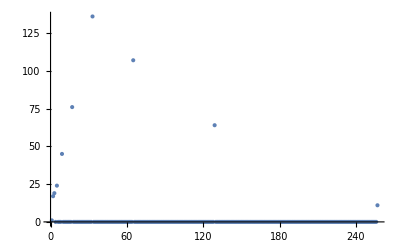

```mathematica
ListPlot[binCountsList]
```

Answer the following in the text cell below. Is every possible value of lambda that was passed in used for at least one of the genes? You will have to look at the bin counts directly here as some things may be too small to see on the plot above. Which value of lambda is used for the most different target genes? Given the shape of the curve, would you expect adding larger or smaller values of lambda, outside the range tried, would improve the results? For how many genes do you think the coefficients might change if we added 512 to the end of the list of lambdas passed in, and why?

```mathematica
Normal[binCountsList]
```

{1,17,19,0,24,0,0,0,45,0,0,0,0,0,0,0,76,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,136,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,107,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,11}

Write your answer here. 
>> Not all the possible lambda values have been used. Most commonly used lambda vaues is  32, with 136 times. Since the larger lambda values are less used, I would expect little or no improvement in results. However, since the gap between 512 and 256 is large compared to the range of commonly used lambda values, I would expect less than 11 coefficient to change, with reason being that the trend of lambda usage decreases from 32.

What other ways of determining which lambda values to try might work better than the approach used in the large test?

Rather than a series whose terms are the successive powers of two, other variations of collection of lambda values could be tried.

### Results and accuracy

Above,  you computed the frequency distribution of the lambdas chosen using BinCounts. Now use a similar approach to compute the distribution, across target genes, of the number of non-zero coefficients (i.e. the maximum number of potential regulators of each TF, according to the LASSO method used here). If you want to visualize it, I suggest using BarChart instead of ListPlot.

This make take a couple of lines of code -- I used several nested Maps.

Remember that netObject["edgeScores"] contains the coefficients from the regressions in the form of SparseArray objects, so you may want to map Normal across them first to get an ordinary matrix.

```mathematica
ct= ConstantArray[0, Length[netObject["edgeScores"]]]
```

```mathematica
Do[
Map[ If[# ≠ 0, ct[[i]]++] &, netObject["edgeScores"][[i]]],
		{i, Length[netObject["edgeScores"]]}
];
```

```mathematica
ct
```

{0,0,1,0,0,1,1,7,0,0,3,1,0,0,0,0,0,0,0,2,2,4,4,0,0,7,1,5,12,0,9,12,9,8,0,0,11,0,0,1,4,4,0,3,0,11,4,1,8,3,0,0,0,1,0,4,9,1,11,0,2,0,9,4,0,1,0,1,0,1,11,0,0,3,3,10,0,3,1,0,1,0,0,3,1,0,13,3,4,0,6,11,1,0,4,1,0,0,2,0,0,0,0,0,4,1,0,12,4,2,5,0,0,0,3,0,0,1,0,0,3,0,0,8,5,0,0,0,5,5,0,9,6,4,3,3,5,3,0,0,1,5,2,3,9,9,5,0,4,0,1,0,1,5,1,4,2,4,0,1,4,0,0,6,1,1,3,0,0,1,0,2,2,0,1,0,0,1,1,4,3,12,1,0,1,1,3,12,0,1,0,13,1,0,3,2,10,0,0,6,11,0,0,3,2,0,0,0,1,3,1,1,0,0,5,0,0,2,1,1,8,0,0,1,9,0,0,10,0,11,2,10,10,5,5,1,11,0,2,5,0,9,7,4,0,0,1,0,0,0,0,3,0,13,1,10,0,0,2,2,0,0,8,0,4,1,2,0,0,1,0,5,8,3,0,1,1,11,0,1,0,1,9,0,2,0,8,5,0,10,0,1,7,11,1,0,0,3,2,0,0,0,0,0,10,0,1,1,0,0,0,7,1,1,0,0,0,0,1,0,3,1,0,0,1,0,0,1,0,2,1,0,1,0,1,1,0,0,0,1,2,0,8,0,0,1,3,1,0,1,2,2,10,1,0,0,0,12,0,0,14,2,1,1,0,0,0,1,1,7,1,0,1,0,0,1,3,0,0,0,3,0,0,0,0,1,5,3,0,3,1,0,1,6,4,0,0,0,11,0,0,8,11,3,10,0,0,2,0,5,11,3,0,0,2,9,2,0,0,0,0,0,0,0,0,0,0,1,0,1,3,2,0,9,0,2,10,4,4,0,8,0,5,4,0,0,0,0,3,4,0,3,9,3,1,0,0,0,4,0,1,7,0,0,0,5,0,0,8,1,1,2,0,1,0,0,0,1,0,0,0,0,1,1,4,8,0,0,10,0,2,0,10,1,0,0,3,0,9,0}

```mathematica
temp2 = BinCounts[ct, {0, Max[ct]+1}]
```

{224,90,31,36,26,19,5,7,12,14,13,13,6,3,1}

```mathematica
N[224/Total[temp2]]
```

0.448

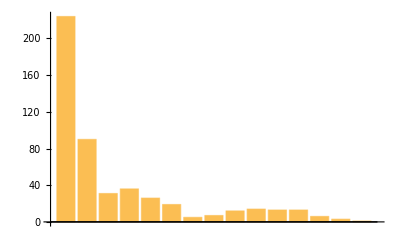

```mathematica
BarChart[temp2]
```

What is the most common number of TFs with non-zero coefficients, across all target genes? About what fraction of genes have that most common number? Do any genes have non-zero coefficients for all 14 TFs? What do you think about these observations? Take a minute to think an write down a comment and/or a thoughtful question.

The most common coefficient with non-zero count is 0, which occupies about 44.8%. There is only one gene that have non-zero coefficients for all 14 TFs. The high number of 0 makes me think that most genes are not associated with the TFs.

The provided code function presentNetAccuracy (which eventually calls your evalEdges) prints out two plots. Call it below on the netObject you have been studying and the path to the binding data file “Test/calling_cards_binary.csv” (keep in mind that this notebook is not in the “Test” directory, so it may be convenient to set the working directory first.). Below the graphs, please comment on the results.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\choyo\Documents\Wolfram Mathematica\netRegression-Dist-1.01\Test

```mathematica
input = calling_cards_binary.csv
```

_binary.csv calling_cards

```mathematica
input
```

_binary.csv calling_cards

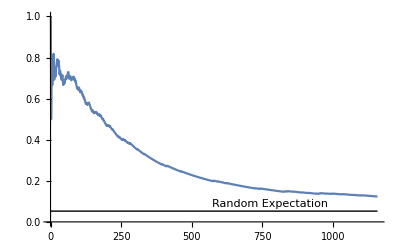
-Graphics-Edge Rank ThresholdPrecision (Fraction of edges supported)

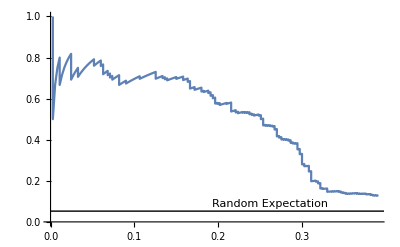
-Graphics-RecallPrecision (Fraction of edges supported)

```mathematica
presentNetAccuracy[netObject,"calling_cards_binary.csv"]
```

```mathematica
Precision converges for both recall and edge rank threshold.
```

Does this method of network inference from gene expression data actually work, given the type of gene expression data we provided (taken at time points shortly after direct perturbation of a TF)?

It works, but it has some limitations. For instance, precision converging to around ~0.1 to 0.2 indicates only 10~20% of predicted values would be correct.

Approximately what fraction of the top 200 edges are supported by the binding data?

About 50% of the top 200 edges are supported.

When the rank threshold for predicting an edge is such that about 20% of the edges in the binding data are predicted, what fraction of the predicted edges are supported by the binding data (roughly)?

20% of the edges are yielded for the top 600 edges. This is about 60%.

## Extra credit (1 point)

Copy the code file netRegression.m into a new file called singleLambda.m. Implement a version that chooses a single lambda for all target genes, taking into account the cross-validation error of all genes given that lambda. This is roughly speaking just a matter of switching the order of the maps over genes and lambda values, plus totaling the cross-validation error across all genes before choosing lambda. If you are writing a lot of new code, you’re probably doing this the hard way. Make sure to rename your functions so they don’t clobber the original versions and delete any functions from your code file that don’t need to be changed.

Evaluate the results (e.g. by calling presentNetAccuracy) and compare them to the results of the original code (i.e. the answers to the questions above). Do you think choosing a single lambda is a good idea? Does it improve the results, make them worse, or make minimal difference? If it improves the results (and I’m not saying it will), why do you think that might be?

## Rubric

One point for a correct implementation of constructErrorsMatrix, regardless of any other functions or questions.

Two points for correct implementation of netLasso, which requires correct implementation of constructErrorsMatrix and choosLambda.

One point for a correct implementation of evalEdges, regardless of any other functions or questions.

One point for correct / appropriate answers to the questions regarding lambdas chosen. Partial credit is possible.

One point for correct / appropriate answers to the questions regarding results and accuracy. Partial credit is possible.